```mathematica
<<Wolfram`QuantumFramework`
```

### 11.1 [BSc] How do I build the Bell, GHZ, and W states?

WL:

Bell state  1/(√2)(|00⟩ + |11⟩):

```mathematica
phiPlus =With[{zero={1,0},one={0,1}},Normalize@Flatten[KroneckerProduct[zero,zero]+KroneckerProduct[one,one]]]
```

{1/(√2),0,0,1/(√2)}

All Bell states:

```mathematica
bells=Table[KroneckerProduct[IdentityMatrix[2],PauliMatrix[k]].phiPlus,{k,0,3}]
```

{{1/(√2),0,0,1/(√2)},{0,1/(√2),1/(√2),0},{0,ⅈ/(√2),-ⅈ/(√2),0},{1/(√2),0,0,-1/(√2)}}

GHZ state 1/(√2)(|000⟩ + |111⟩):

```mathematica
With[{zero={1,0},one={0,1}},Normalize@Flatten[KroneckerProduct[zero,zero,zero]+KroneckerProduct[one,one,one]]]
```

{1/(√2),0,0,0,0,0,0,1/(√2)}

W state   1/(√3)(|001⟩ + |010⟩ + |100⟩) :

```mathematica
With[{zero={1,0},one={0,1}},Normalize@Total[Flatten/@KroneckerProduct@@@Permutations[{zero,zero,one}]]]
```

{0,1/(√3),1/(√3),0,1/(√3),0,0,0}

QF:

Build Bell states:

```mathematica
bellQF=QuantumState/@{"PhiPlus","PsiPlus","PsiMinus","PhiMinus"}
```

{1/(√2)00+1/(√2)11,1/(√2)01+1/(√2)10,1/(√2)01-1/(√2)10,1/(√2)00-1/(√2)11}

Verify the Bell state equality:

```mathematica
MapThread[QuantumState[#1]==#2&,{bells,bellQF}]
```

{True,True,True,True}

Other requested states:

```mathematica
TraditionalForm[states =QuantumState/@{"Bell","GHZ","W"}]
```

{1/(√2)00+1/(√2)11,1/(√2)000+1/(√2)111,1/(√3)001+1/(√3)010+1/(√3)100}

```mathematica
Normal[#["StateVector"]]&/@states
```

{{1/(√2),0,0,1/(√2)},{1/(√2),0,0,0,0,0,0,1/(√2)},{0,1/(√3),1/(√3),0,1/(√3),0,0,0}}

Circuits that prepare Bell and GHZ states(already named circuits):

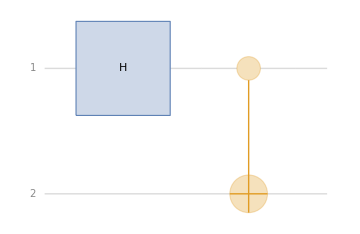

```mathematica
QuantumCircuitOperator["Bell"]["Diagram"]
```

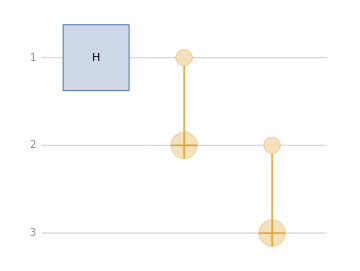

```mathematica
QuantumCircuitOperator["GHZ"]["Diagram"]
```

Define the circuit the prepares the W state:

```mathematica
qc =QuantumCircuitOperator[{"RY"[2 ArcCos[1/√3]],"CH","CNOT"->{2,3},"CNOT","X"}];
```

Visualize the circuit:

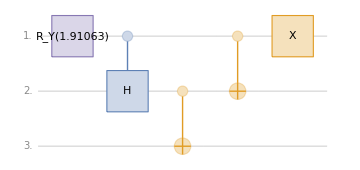

```mathematica
N@qc["Diagram"]
```

```mathematica
qc[]==QuantumState["W"]
```

True

### 11.2 [BSc] How do I measure a Bell pair jointly and exhibit the perfect correlations?

WL:

Define the PhiPlus state:

```mathematica
phiPlus=With[{zero={1,0},one={0,1}},Normalize@Flatten[KroneckerProduct[zero,zero]+KroneckerProduct[one,one]]];
```

Joint Born probabilities:

```mathematica
Abs[phiPlus]^2
```

{1/2,0,0,1/2}

Each qubit on its own is unbiased, summing the joint distribution over the second label leaves the marginal of the first:

```mathematica
Total[Partition[Abs[phiPlus]^2,2]]
```

{1/2,1/2}

The correlators are expectation values of the three parity observables σ_k⊗ σ_k:

```mathematica
Table[Conjugate[phiPlus].KroneckerProduct[PauliMatrix[k],PauliMatrix[k]].phiPlus,{k,3}]
```

{1,-1,1}

Measuring both qubits in the X basis instead means rotating by a Hadamard on each side first and reading the same four probabilities:

```mathematica
Abs[KroneckerProduct[HadamardMatrix[2],HadamardMatrix[2]].phiPlus]^2
```

{1/2,0,0,1/2}

QF:

Measuring the wire list is the joint computational measurement, it returns a QuantumMeasurement object:

```mathematica
qm=QuantumMeasurementOperator[{1,2}][QuantumState["PhiPlus"]]
```

QuantumMeasurement[…]

```mathematica
qm["Probabilities"]
```

<|00→1/2,01→0,10→0,11→1/2|>

The correlators come from measuring the two-qubit parity observables, whose names are the two letters Pauli strings:

```mathematica
Table[QuantumMeasurementOperator[QuantumOperator[StringRepeat[s,2]]][QuantumState["PhiPlus"]]["Mean"],{s,{"X","Y","Z"}}]
```

{1,-1,1}

```mathematica
Values[qm["Probabilities"]]==Abs[phiPlus]^2
```

True

Both give one half on |00⟩ and |11⟩ and zero on mixed outcomes, and correlators +1 for XX,ZZ and -1 for YY

### 11.3 [BSc] How do I compute the Schmidt decomposition and Schmidt rank of a bipartite pure state?

WL:

Take a fully general two-qubit state and reshape its four amplitudes into the coefficient matrix:

```mathematica
c=ArrayReshape[{a,b,c,d},{2,2}]
```

{{a,b},{c,d}}

The Schmidt coefficients are the singular values, that is the square roots of the eigenvalues of C C^†:

```mathematica
Simplify@Sqrt@Eigenvalues[c.ConjugateTranspose[c]]
```

{1/(√2)(√(a Conjugate[a]+b Conjugate[b]+c Conjugate[c]+d Conjugate[d]-√((a Conjugate[a]+b Conjugate[b]+c Conjugate[c]+d Conjugate[d])^2-4 (b c-a d) (Conjugate[b] Conjugate[c]-Conjugate[a] Conjugate[d])))),1/(√2)(√(a Conjugate[a]+b Conjugate[b]+c Conjugate[c]+d Conjugate[d]+√((a Conjugate[a]+b Conjugate[b]+c Conjugate[c]+d Conjugate[d])^2-4 (b c-a d) (Conjugate[b] Conjugate[c]-Conjugate[a] Conjugate[d]))))}

The determinant sits under the inner square root, so the smaller coefficient vanishes exactly when the determinant does. The Schmidt rank is therefore the rank of the coefficient matrix:

```mathematica
{MatrixRank[c],Det[c]}
```

{2,-b c+a d}

Imposing a vanishing determinant collapses the rank to one, the product case:

```mathematica
MatrixRank[c/. d->b c/a]
```

1

For a worked instance take the state whose three terms are |00⟩, |01⟩ and |10⟩ ; whose two Schmidt coefficients come out unequal:

```mathematica
psi=With[{zero={1,0},one={0,1}},Normalize@Total[Flatten/@{KroneckerProduct[zero,zero],KroneckerProduct[zero,one],KroneckerProduct[one,zero]}]]
```

{1/(√3),1/(√3),1/(√3),0}

```mathematica
SingularValueList[ArrayReshape[psi,{2,2}]]
```

{√(1/6 (3+√5)),√(1/6 (3-√5))}

```mathematica
Simplify[Total[SingularValueList[ArrayReshape[psi,{2,2}]]^2]]
```

1

QF:

“SchmidtBasis” returns the same state re-expressed in its own Schmidt bases, as a state object carrying those bases:

```mathematica
sb=QuantumState[psi]["SchmidtBasis"]
```

√(1/6 (3+√5))u_1 v_1+√(1/6 (3-√5))u_2 v_2

```mathematica
TraditionalForm[Simplify@sb["Basis"]]
```

<|u_1 v_1→(((1+√5) (3+√5))/(2 √(2 (5+√5) (5+2 √5))) | (3+√5)/(√(2 (5+√5) (5+2 √5)))
(1+√5)^2/(2 √(2 (5+√5) (5+2 √5))) | (1+√5)/(√(2 (5+√5) (5+2 √5)))),u_1 v_2→(((1-√5) (3+√5))/(2 √((10-2 √5) (5+2 √5))) | 1/2 (3+√5) √((5+√5)/(10 (5+2 √5)))
((1-√5) (1+√5))/(2 √((10-2 √5) (5+2 √5))) | 1/2 (1+√5) √((5+√5)/(10 (5+2 √5)))),u_2 v_1→(((3-√5) (1+√5))/(2 √(2 (5-2 √5) (5+√5))) | (3-√5)/(√(2 (5-2 √5) (5+√5)))
((1-√5) (1+√5))/(2 √(2 (5-2 √5) (5+√5))) | (1-√5)/(√(2 (5-2 √5) (5+√5)))),u_2 v_2→(((1-√5) (3-√5))/(2 √((5-2 √5) (10-2 √5))) | 1/2 (3-√5) √((5+√5)/(10 (5-2 √5)))
(1-√5)^2/(2 √((5-2 √5) (10-2 √5))) | 1/2 (1-√5) √((5+√5)/(10 (5-2 √5))))|>

In that basis the amplitude vector is diagonal: the coefficients sit on the matched pairs and everything else is zero:

```mathematica
Normal[sb["StateVector"]]
```

{√(1/6 (3+√5)),0,0,√(1/6 (3-√5))}

The Schmidt rank is the number of surviving amplitudes:

```mathematica
Count[Normal[sb["StateVector"]],Except[0]]
```

2

“SchmidtDecompose” renders the decomposition as the sum of Kronecker products itself:

```mathematica
QuantumState[psi]["SchmidtDecompose"]//FullSimplify
```

1/(√10)(√(3-√5) ((1/(√3)+(1-√5)/(2 √3))/(√(1/12 (-1+√5)^2+(1/(√3)+(1-√5)/(2 √3))^2)) | (1-√5)/(2 √(3 (1/12 (-1+√5)^2+(1/(√3)+(1-√5)/(2 √3))^2)))
0 | 0)⊗((1-√5)/(2 √(1+1/4 (-1+√5)^2)) | 1/(√(1+1/4 (-1+√5)^2))
0 | 0)+√(3+√5) ((1/(√3)+(1+√5)/(2 √3))/(√(1/12 (1+√5)^2+(1/(√3)+(1+√5)/(2 √3))^2)) | (1+√5)/(2 √(3 (1/12 (1+√5)^2+(1/(√3)+(1+√5)/(2 √3))^2)))
0 | 0)⊗((1+√5)/(2 √(1+1/4 (1+√5)^2)) | 1/(√(1+1/4 (1+√5)^2))
0 | 0))

A product input collapses to a single term, the rank-one case:

```mathematica
sb2=(QuantumState["00"]+QuantumState["10"])["Normalize"]["SchmidtBasis"]
```

u_1 v_1

```mathematica
Count[Normal[sb2["StateVector"]],Except[0]]
```

1

Both give the coefficients and rank dropping to rank 1 on a product state. Reshape-plus-SVD returns bare numbers, while the framework returns the state itself in its Schmidt bases, so the local bases that realize the decomposition come along with the coefficients:

```mathematica
DeleteCases[Normal[sb["StateVector"]],0]==SingularValueList[ArrayReshape[psi,{2,2}]]
```

True

### 11.4 [BSc] How do I quantify pure-state entanglement by the entropy of entanglement (the von Neumann entropy of a reduced state)?

WL:

For a pure bipartite state the entanglement is measured by the von Neumann entropy of either reduced state, which in terms of the Schmidt coefficients is the Shannon entropy of their squares. It is zero for a product state and log_2 d for a maximally entangled one. Every two-qubit pure state is, up to local unitaries, 
cosθ ∣00⟩ + sinθ∣11⟩, so that one-parameter family carries the whole answer.

Build the family of density matrices from the ket:

```mathematica
ket=With[{zero={1,0},one={0,1}},Cos[θ] Flatten[KroneckerProduct[zero,zero]]+Sin[θ] Flatten[KroneckerProduct[one,one]]]
```

{Cos[θ],0,0,Sin[θ]}

Compute ρ_A the reduced density matrix, contracting the reshaped density matrix:

```mathematica
rhoA=Simplify[TensorContract[ArrayReshape[KroneckerProduct[ket,Conjugate[ket]],{2,2,2,2}],{{2,4}}],θ∈Reals]
```

{{Cos[θ]^2,0},{0,Sin[θ]^2}}

Its two eigenvalues are the Schmidt weights,  feed them to the entropy sum:

```mathematica
s=Simplify[-Total[# Log2[#]&/@Eigenvalues[rhoA]],0<θ<Pi/2]
```

-(2 (Cos[θ]^2 Log[Cos[θ]]+Log[Sin[θ]] Sin[θ]^2))/Log[2]

Maximizing over the family locates the maximally entangled point:

```mathematica
Simplify@Maximize[{s,0<θ<Pi/2},θ]
```

{1,{θ→π/4}}

QF:

Trace out qubit  and ask the reduced state for its “VonNeumannEntropy”, which comes back as a Quantity in bits:

```mathematica
redA = QuantumPartialTrace[QuantumState[ket], {2}];
```

```mathematica
Simplify[redA["VonNeumannEntropy"],0<θ<Pi/2]
```

-(2 (Cos[θ]^2 Log[Cos[θ]]+Log[Sin[θ]] Sin[θ]^2))/Log[2] b

```mathematica
Simplify[redA["VonNeumannEntropy"]==Quantity[s,"Bits"],0<θ<Pi/2]
```

True

The packaged monotone reads the same number off the state directly:

```mathematica
entangEntrop =Simplify[QuantumEntanglementMonotone[QuantumState[ket],"EntanglementEntropy"],0<θ<π/2]
```

-(2 (Cos[θ]^2 Log[Cos[θ]]+Log[Sin[θ]] Sin[θ]^2))/Log[2] b

```mathematica
QuantityMagnitude@entangEntrop == s
```

True

### 11.5 [BSc] How do I verify no-signalling through the invariance of reduced states?

Whatever Bob does to his qubit alone, Alice’s reduced state is unchanged: for a unitary because the unitary and its adjoint meet under the trace over Bob’s factor, and for a measurement Bob does not report because the non-selective Lüders sum contracts to the same thing. Since Alice’s statistics are fixed by her reduced state, no choice Bob makes can carry information to her. The claim is linear in the joint state, so a generic  4×4 array with nothing assumed about it already settles it for every state.

WL:

Take a generic two-qubit operator and its reduction over B:

```mathematica
r=Array[Subscript[r,##]&,{4,4}]
```

{{r_(1,1),r_(1,2),r_(1,3),r_(1,4)},{r_(2,1),r_(2,2),r_(2,3),r_(2,4)},{r_(3,1),r_(3,2),r_(3,3),r_(3,4)},{r_(4,1),r_(4,2),r_(4,3),r_(4,4)}}

```mathematica
rhoA=TensorContract[ArrayReshape[r,{2,2,2,2}],{{2,4}}]
```

{{r_(1,1)+r_(2,2),r_(1,3)+r_(2,4)},{r_(3,1)+r_(4,2),r_(3,3)+r_(4,4)}}

A general single-qubit unitary is the  Z Y Z Euler product, with three free angles:

```mathematica
u=MatrixExp[-I ϕ PauliMatrix[3]/2].MatrixExp[-I θ PauliMatrix[2]/2].MatrixExp[-I λ PauliMatrix[3]/2]
```

{{ⅇ^(-(ⅈ λ)/2-(ⅈ ϕ)/2) Cos[θ/2],-ⅇ^((ⅈ λ)/2-(ⅈ ϕ)/2) Sin[θ/2]},{ⅇ^(-(ⅈ λ)/2+(ⅈ ϕ)/2) Sin[θ/2],ⅇ^((ⅈ λ)/2+(ⅈ ϕ)/2) Cos[θ/2]}}

Act with it on qubit  B only and reduce again, compare it with ρ_A:

```mathematica
FullSimplify[TensorContract[ArrayReshape[KroneckerProduct[IdentityMatrix[2],u].r.ConjugateTranspose[KroneckerProduct[IdentityMatrix[2],u]],{2,2,2,2}],{{2,4}}]==rhoA,{θ,ϕ,λ}∈Reals]
```

True

Now let Bob measure along an arbitrary axis, using the two projectors (I± n̂ . σ⃗) and reduce the mixture:

```mathematica
lueders=Sum[KroneckerProduct[IdentityMatrix[2],proj].r.KroneckerProduct[IdentityMatrix[2],proj],{proj,(IdentityMatrix[2]+# FromSphericalCoordinates[{1,θ1,ϕ1}].PauliMatrix[{1,2,3}])/2&/@{1,-1}}];
```

```mathematica
FullSimplify[TensorContract[ArrayReshape[lueders,{2,2,2,2}],{{2,4}}]==rhoA,{θ1,ϕ1}∈Reals]
```

True

QF:

The same generic array as a two-qubit state object, with the framework’s own general single-qubit unitary “U3” placed on wire 2:

```mathematica
qr=QuantumState[r,{2,2}]
```

QuantumState[…]

```mathematica
FullSimplify[QuantumPartialTrace[QuantumOperator["U3"[θ,ϕ,λ],{2}][qr],{2}]-QuantumPartialTrace[qr,{2}],{θ,ϕ,λ}∈Reals]
```

0

For the unreported measurement, build the two projectors as operators on wire 2 and sum their action on the state:

```mathematica
lu=Total@Table[(1/2 QuantumOperator["I"+ s "U3"[2 θ1,ϕ1,π-ϕ1],{2}])[qr],{s,{1,-1}}];
```

```mathematica
FullSimplify[QuantumPartialTrace[lu,{2}]-QuantumPartialTrace[qr,{2}],{θ1,ϕ1}∈Reals]
```

0

Every check returns True(or 0), for an arbitrary joint state, an arbitrary local unitary, and an arbitrary measurement axis. Entanglement therefore correlates outcomes without transmitting anything: Alice sees exactly the same statistics whether Bob acts, measures, or does nothing, and the correlations only appear when the two records are later compared.

### 11.6 [MSc] How do I test a mixed state for entanglement by the positive-partial-transpose (Peres-Horodecki) criterion?

Transposing only Bob’s factor of a separable state sends each of its product terms to another product term, so the result is still a legitimate state and its spectrum stays nonnegative. A negative eigenvalue of the partial transpose therefore certifies entanglement. Take the family ρ(q)=q |Φ^+⟩⟨Φ^+| + (1-q) |01⟩⟨01| separable at q=0 and a Bell state at q=1

WL:

Build the family:

```mathematica
rho=With[{zero={1,0},one={0,1}},With[{bell=Normalize@Flatten[KroneckerProduct[zero,zero]+KroneckerProduct[one,one]],ket01=Flatten@KroneckerProduct[zero,one]},q KroneckerProduct[bell,bell]+(1-q) KroneckerProduct[ket01,ket01]]]
```

{{q/2,0,0,q/2},{0,1-q,0,0},{0,0,0,0},{q/2,0,0,q/2}}

The partial transpose on B  reshapes the matrix into its four legs and exchanges the two belonging to B:

```mathematica
pt=ArrayReshape[Transpose[ArrayReshape[rho,{2,2,2,2}],{1,4,3,2}],{4,4}];
```

```mathematica
eigs=FullSimplify[Eigenvalues[pt],0<=q<=1]
```

{q/2,q/2,1/2 (1-q-√(1+2 (-1+q) q)),1/2 (1-q+√(1+2 (-1+q) q))}

Demanding that all four be nonnegative locates the entire positive-partial-transpose region of the family:

```mathematica
Reduce[And@@Thread[eigs>=0]&&0<=q<=1,q,Reals]
```

q==0

QF:

QuantumPartialTranspose transposes the listed qudits and hands back a state object, whose spectrum reads off directly:

```mathematica
ptQF=QuantumPartialTranspose[QuantumState[rho,{2,2}],{2}]
```

q/2 0000+(1-q)0101+q/2 0110+q/2 1001+q/2 1111

```mathematica
Simplify[ptQF["Eigenvalues"]-eigs]
```

{0,0,0,0}

```mathematica
Table[QuantumEntangledQ[QuantumState[rho/. q->v,{2,2}],Automatic,"Negativity"],{v,{0,1/4,1/2,1}}]
```

{False,True,True,True}

Both give the same spectrum {q/2,q/2,1/2 (1-q-√(1+2 (-1+q) q)),1/2 (1-q+√(1+2 (-1+q) q))}, whose third entry is negative for every q>0 the only member of the family with a positive partial transpose is the separable endpoint q=0

### 11.7 [MSc] How do I compute the concurrence and the negativity of a mixed two-qubit state?

Both turn the criterion of 11.6 into a number. The negativity is half the amount by which the trace norm of the partial transpose exceeds one, that is the total weight of the negative part of its spectrum. The concurrence is Wootters’ formula: with λ_1>=λ_2>=λ_3>=λ_4 the square roots of the eigenvalues of ρ times its spin flip
(σ_y⊗ σ_y)ρ*(σ_y⊗ σ_y),  the concurrence is max(0, λ_1-λ_2-λ_3-λ_4). Use the same family as in 11.6.

WL:

Define the family:

```mathematica
rho=With[{zero={1,0},one={0,1}},With[{bell=Normalize@Flatten[KroneckerProduct[zero,zero]+KroneckerProduct[one,one]],ket01=Flatten@KroneckerProduct[zero,one]},q KroneckerProduct[bell,bell]+(1-q) KroneckerProduct[ket01,ket01]]]
```

{{q/2,0,0,q/2},{0,1-q,0,0},{0,0,0,0},{q/2,0,0,q/2}}

```mathematica
flipped=KroneckerProduct[PauliMatrix[2],PauliMatrix[2]].Conjugate[rho].KroneckerProduct[PauliMatrix[2],PauliMatrix[2]];
```

The four λ_i are the square roots of the spectrum of the product:

```mathematica
lambdas=Simplify[Sqrt@Eigenvalues[rho.flipped],0<q<1];
```

Compute concurrence:

```mathematica
concurrence=Simplify[Max[0,2 Max[lambdas]-Total[lambdas]],0<q<1]
```

q

Compute negativity:

```mathematica
negativity=Simplify[(Total[Abs[Eigenvalues@ArrayReshape[Transpose[ArrayReshape[rho,{2,2,2,2}],{1,4,3,2}],{4,4}]]]-1)/2,0<q<1]
```

1/2 (-1+q+√(1-2 q+2 q^2))

QF:

```mathematica
negQF=QuantumEntanglementMonotone[QuantumState[rho,{2,2}],"Negativity"];
```

Check after simplifying nested radicals:

```mathematica
Simplify[negQF==negativity,0<q<1]
```

True

Calculate the concurrence:

```mathematica
concu =Simplify[QuantumEntanglementMonotone[QuantumState[rho,{2,2}],"Concurrence"],0<q<1]
```

q

Plot the metrics:

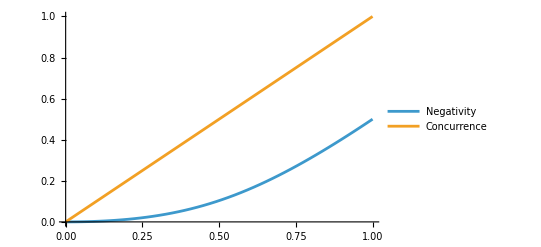

```mathematica
Plot[{negQF,concu},{q,0,1},PlotLegends->{"Negativity","Concurrence"}]
```

Both give concurrence exactly q linear in the Bell admixture reaching 1 on the Bell state, and negativity 1/2 (-1+q+√(1-2 q+2 q^2)) which is likewise positive for every q>0 but smaller than concurrence reaching one half at q=1. The two measures vanish together and order the family the same way, yet they are different functions: neither is a rescaling of the other, and only the concurrence reaches  1 on a maximally entangled state.

### 11.8 [MSc] How do I construct an entanglement witness for a given entangled state?

A witness is a Hermitian operator W whose expectation value is nonnegative on every separable state and negative on the target, so one measured number certifies entanglement. When the partial transpose of the target has a negative eigenvalue with eigenvector |e⟩, the choice W=(|e⟩⟨e|)^T_B works, transposing back inside the trace turns Tr[W ρ] into ⟨e|ρ^T_B|e⟩ which is that negative eigenvalue, while on a product state W cannot go negative. Build it for the Bell state |Φ^+⟩

WL:

Target state:

```mathematica
rho=With[{zero={1,0},one={0,1}},KroneckerProduct[#,#]&@Normalize@Flatten[KroneckerProduct[zero,zero]+KroneckerProduct[one,one]]];
```

```mathematica
es=Eigensystem[ArrayReshape[Transpose[ArrayReshape[rho,{2,2,2,2}],{1,4,3,2}],{4,4}]];
```

Pick the eigenvector belonging to the negative eigenvalue:

```mathematica
e=Normalize@First@Pick[es[[2]],Negative/@es[[1]]]
```

{0,-1/(√2),1/(√2),0}

Transposing its projector back on the B factor gives the witness:

```mathematica
wit=ArrayReshape[Transpose[ArrayReshape[KroneckerProduct[e,Conjugate[e]],{2,2,2,2}],{1,4,3,2}],{4,4}];
```

On the target it returns the negative eigenvalue itself:

```mathematica
Tr[wit.rho]
```

-1/2

On a general product state, each factor carried by its own pair of Bloch angles, the expectation value has a closed form:

```mathematica
expW=FullSimplify@ComplexExpand@Re[Conjugate[#].wit.#&@Flatten@KroneckerProduct[{Cos[θa/2],Exp[I ϕa] Sin[θa/2]},{Cos[θb/2],Exp[I ϕb] Sin[θb/2]}]]
```

1/4 (1-Cos[θa] Cos[θb]-Cos[ϕa+ϕb] Sin[θa] Sin[θb])

Searching that expression for a negative value over the whole product-state manifold comes up empty, so no product state, and by convexity no separable state, is flagged:

```mathematica
Reduce[expW<0&&0<=θa<=Pi&&0<=θb<=Pi,{θa,ϕa,θb,ϕb},Reals]
```

False

QF:

Getting the witness:

```mathematica
witQF=QuantumState["PsiMinus"]["Transpose",{2}]["Operator"]
```

QuantumOperator[…]

```mathematica
Normal[witQF["Matrix"]]==wit
```

True

Measuring that observable on the target gives its expectation value:

```mathematica
QuantumMeasurementOperator[witQF][QuantumState["PhiPlus"]]["Mean"]
```

-1/2

And on a general product state, the same closed form:

```mathematica
FullSimplify[QuantumCircuitOperator[{"U3"[θa,ϕa,0]->1,"U3"[θb,ϕb,0]->2,QuantumMeasurementOperator[witQF]}][]["Mean"]==expW,{θa,ϕa,θb,ϕb}∈Reals]
```

True

Both give the same witness, with expectation value -1/2 on the Bell state, and on product states the closed form (1-n_a·n_b)/4, which is nonnegative because a dot product of unit vectors never exceeds one, and vanishes exactly on the aligned product states. So a single Hermitian observable, measurable without any tomography, separates this entangled state from every separable one; the price is that the witness is tailored to the target, and a different entangled state generally needs a different one.

### 11.9 [MSc] How do I decide whether a pure state can be converted to another by LOCC (Nielsen’s theorem)?

Nielsen’s theorem: one pure state can be turned into another with certainty by local operations and classical communication if and only if the first state’s vector of Schmidt weights, the squared Schmidt coefficients sorted decreasing, is majorized by the second’s. Majorized means every partial sum of the first is at most the corresponding partial sum of the second. Flatter weights mean more entanglement, and LOCC can only steepen them. Take two states of two qutrits with weights
{1/2, 3/10, 1/5} and {3/5,1/5,1/5}

WL:

A state with prescribed Schmidt weights is the sum of the matched basis kets ∣kk⟩ weighted by the square roots:

```mathematica
psi=Normalize@Total[Sqrt[{1/2,3/10,1/5}] (Flatten[KroneckerProduct[#,#]]&/@IdentityMatrix[3])];
```

```mathematica
phi=Normalize@Total[Sqrt[{3/5,1/5,1/5}] (Flatten[KroneckerProduct[#,#]]&/@IdentityMatrix[3])];
```

Recover the weights from the states themselves, as the squared singular values of the reshaped amplitudes (11.3):

```mathematica
{lp,lq}=(Sort[SingularValueList[ArrayReshape[#1,{3,3}]]^2,Greater]&)/@{psi,phi}
```

{{1/2,3/10,1/5},{3/5,1/5,1/5}}

Majorization is the comparison of the two partial-sum sequences, checked in both directions:

```mathematica
{And@@Thread[Accumulate[lp]<=Accumulate[lq]],And@@Thread[Accumulate[lq]<=Accumulate[lp]]}
```

{True,False}

The entropies order consistently, since the allowed direction can only lose entanglement:

```mathematica
N[-Total[# Log2[#]&/@#]&/@{lp,lq}]
```

{1.48548,1.37095}

QF:

The Schmidt weights are the probabilities the state reports in its own Schmidt basis:

```mathematica
qpsi=QuantumState[psi,{3,3}]
```

1/(√2)00+√(3/10)11+1/(√5)22

```mathematica
{wp,wq}=Sort[Values[#["SchmidtBasis"]["Probability"]],Greater]&/@{qpsi,QuantumState[phi,{3,3}]}
```

{{1/2,3/10,1/5},{3/5,1/5,1/5}}

```mathematica
{And@@Thread[Accumulate[wp]<=Accumulate[wq]],And@@Thread[Accumulate[wq]<=Accumulate[wp]]}
```

{True,False}

```mathematica
{wp,wq}=={lp,lq}
```

True

Both directions come back true then false: the partial sums 1/2,4/5,1 of the first state never exceed 3/5,4/5,1 of the second , so the first can be converted into the second with certainty, while the reverse fails at the very first sum, since 3/5 exceeds 1/2. The conversion is one-way. The entropies, about 1.485 and 1.371 bits order the same way as they must. Majorization is a whole chain of inequalities, and two states can be ordered by entropy while neither majorizes the other, in which case no certain conversion exists in either direction.

### 11.10 [MSc] How do I verify monogamy of entanglement (the CKW inequality) using the three-qubit tangle?

Entanglement cannot be freely shared, if A is strongly entangled with B it has little left for C. The Coffman-Kundu-Wootters inequality makes this quantitative. The tangle across the A versus B C  cut is τ_(A |B C)=4det(ρ_a) which for a qubit is the same as 2(1 - Tr ρ_a^2) and it is at least the sum of the squared Wootters concurrences of the two pairs C_AB^2+C_AC^2 . The W and GHZ states sit at the two extremes.

WL:

Both states at once, so the contrast is carried through every step:

```mathematica
states=With[{zero={1,0},one={0,1}},<|"W"->Normalize@Total[Flatten/@(KroneckerProduct@@@Permutations[{zero,zero,one}])],"GHZ"->Normalize@Flatten[KroneckerProduct[zero,zero,zero]+KroneckerProduct[one,one,one]]|>]
```

<|W→{0,1/(√3),1/(√3),0,1/(√3),0,0,0},GHZ→{1/(√2),0,0,0,0,0,0,1/(√2)}|>

The tangle across the cut needs the single-qubit reduction, obtained by contracting the ket-bra leg pairs of qubits 2 and 3:

```mathematica
tangle=4 Det@ArrayReshape[TensorContract[ArrayReshape[KroneckerProduct[#,Conjugate[#]],ConstantArray[2,6]],{{2,5},{3,6}}],{2,2}]&/@states
```

<|W→8/9,GHZ→1|>

The pairwise concurrences come from the two-qubit reductions: dropping qubit  3 leaves the pair AB, dropping qubit 2 leaves AC, and each is fed to Wootters’ formula:

```mathematica
concurrences=(Table[With[{r=ArrayReshape[TensorContract[ArrayReshape[KroneckerProduct[#1,Conjugate[#1]],ConstantArray[2,6]],{{k,k+3}}],{4,4}],y=KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]},With[{l=ReverseSort[√Chop[Re[Eigenvalues[r.y.Conjugate[r].y]]]]},Max[0,First[l]-Total[Rest[l]]]]],{k,{3,2}}]&)/@states
```

<|W→{2/3,2/3},GHZ→{0,0}|>

The slack in the inequality is the tangle minus what the two pairs account for:

```mathematica
residual=tangle-Total/@(concurrences^2)
```

<|W→0,GHZ→1|>

```mathematica
NonNegative/@residual
```

<|W→True,GHZ→True|>

QF:

```mathematica
qstates=<|"W"->QuantumState["W"],"GHZ"->QuantumState["GHZ"]|>
```

<|W→QuantumState[…],GHZ→QuantumState[…]|>

The tangle across a cut is the square of the concurrence for that bipartition, which the framework computes when the bipartition is given explicitly:

```mathematica
tangleQF=(QuantumEntanglementMonotone[#1,{{1},{2,3}},"Concurrence"]^2&)/@qstates
```

<|W→8/9,GHZ→1|>

The pairwise concurrences are the same monotone on the traced-down two-qubit states:

```mathematica
concQF=Table[QuantumEntanglementMonotone[QuantumPartialTrace[#,{k}],"Concurrence"],{k,{3,2}}]&/@qstates
```

<|W→{2/3,2/3},GHZ→{0,0}|>

```mathematica
{tangleQF==tangle,concQF==concurrences}
```

{True,True}

For the W state the tangle is  8/9 and both pairwise concurrences are  2/3, so the two squares add to exactly 8/9: the inequality is saturated, and W distributes all of qubit A’s entanglement into pairwise sharing. For GHZ the tangle is  1 while both pairwise concurrences vanish, so the slack is a full 1: every pair of GHZ qubits is separable once the third is traced out, and all the entanglement is irreducibly three-way.

### 11.11 [MSc] How do I distinguish the GHZ and W classes of tripartite entanglement under SLOCC?

Three qubits have two inequivalent kinds of genuine entanglement, and the residual of the monogamy inequality separates them: the three-tangle is positive on the GHZ class and zero on the W class. It equals four times the modulus of Cayley’s hyperdeterminant of the amplitude tensor, and for a 
2×2×2 tensor that hyperdeterminant has a short form: writing the tensor as two square slices M_0 and M_1, can be computed as discriminant in x of the quadratic det(M_0+x M_1). Being a degree-four invariant, it can only be rescaled by an invertible local map, so its vanishing is a property of the whole SLOCC class.

WL:

```mathematica
states=With[{zero={1,0},one={0,1}},<|"W"->Normalize@Total[Flatten/@(KroneckerProduct@@@Permutations[{zero,zero,one}])],"GHZ"->Normalize@Flatten[KroneckerProduct[zero,zero,zero]+KroneckerProduct[one,one,one]]|>]
```

<|W→{0,1/(√3),1/(√3),0,1/(√3),0,0,0},GHZ→{1/(√2),0,0,0,0,0,0,1/(√2)}|>

The determinant of the slice combination is a quadratic in x, its discriminant is the hyperdeterminant:

```mathematica
tau3=4 Abs[With[{c=Coefficient[Det[#[[1]]+x #[[2]]],x,{0,1,2}]},c[[2]]^2-4 c[[1]] c[[3]]]&@ArrayReshape[#,{2,2,2}]]&/@states
```

<|W→0,GHZ→1|>

Now apply an invertible but non-unitary local map, one factor per qubit, and renormalize. This moves inside the SLOCC class while leaving the unitary orbit:

```mathematica
slocc=Normalize[KroneckerProduct[{{2,1},{0,1}},{{1,0},{1,3}},{{1,2},{1,1}}].#]&/@states;
```

```mathematica
4 Abs[With[{c=Coefficient[Det[#[[1]]+x #[[2]]],x,{0,1,2}]},c[[2]]^2-4 c[[1]] c[[3]]]&@ArrayReshape[#,{2,2,2}]]&/@slocc
```

<|W→0,GHZ→36/5041|>

QF:

Assemble the same invariant as the monogamy residual, every piece a framework monotone:

```mathematica
qstates=<|"W"->QuantumState["W"[3]],"GHZ"->QuantumState["GHZ"[3]]|>
```

<|W→QuantumState[…],GHZ→QuantumState[…]|>

```mathematica
tau3QF=(QuantumEntanglementMonotone[#1,{{1},{2,3}},"Concurrence"]^2-Total[Table[QuantumEntanglementMonotone[QuantumPartialTrace[#1,{k}],"Concurrence"],{k,{3,2}}]^2]&)/@qstates
```

<|W→0,GHZ→1|>

```mathematica
tau3QF==tau3
```

True

Both give a three-tangle of 1 for GHZ and exactly 0 for W. Under the invertible local map the GHZ value drops to 36/5041, rescaled but still nonzero, while the W value stays exactly 0: no invertible local map takes one to the other, in either direction, so the two states head genuinely different classes. The hyperdeterminant and the monogamy residual are two readings of the same invariant, one from the amplitudes and one from the pairwise entanglement they leave behind.

### 11.12a [MSc] How do I construct a 3×3 PPT-entangled (bound) state?

Beyond the smallest dimensions a positive partial transpose no longer implies separability: there are entangled states whose partial transpose stays positive, and because distillation is local and cannot turn a positive partial transpose negative, no amount of processing extracts a single Bell pair from them. They are bound entangled. The standard construction uses an inextensible product basis, a set of orthonormal product vectors whose orthogonal complement contains no product vector at all. The Tiles basis in 3×3 has five members, and the normalized projector onto its complement is bound entangled.

WL:

The five Tiles vectors, each a Kronecker product of two qutrit combinations built from the qutrit kets:

```mathematica
tiles=Normalize/@(Flatten[KroneckerProduct@@#]&/@With[{u=UnitVector[3,#+1]&},{{u[0],u[0]-u[1]},{u[2],u[1]-u[2]},{u[0]-u[1],u[2]},{u[1]-u[2],u[0]},{u[0]+u[1]+u[2],u[0]+u[1]+u[2]}}])
```

{{1/(√2),-1/(√2),0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1/(√2),-1/(√2)},{0,0,1/(√2),0,0,-1/(√2),0,0,0},{0,0,0,1/(√2),0,0,-1/(√2),0,0},{1/3,1/3,1/3,1/3,1/3,1/3,1/3,1/3,1/3}}

They are orthonormal, so their projector has rank five and the complement has rank four:

```mathematica
Outer[#1.#2&,tiles,tiles,1]==IdentityMatrix[5]
```

True

Normalizing the projector onto that four-dimensional complement gives the candidate state:

```mathematica
rho=(IdentityMatrix[9]-Total[KroneckerProduct[#,#]&/@tiles])/4;
```

```mathematica
{Tr[rho],HermitianMatrixQ[rho],PositiveSemidefiniteMatrixQ[rho]}
```

{1,True,True}

Its partial transpose on the second qutrit has no negative eigenvalue, so the criterion of 11.6 says nothing:

```mathematica
Eigenvalues@ArrayReshape[Transpose[ArrayReshape[rho,{3,3,3,3}],{1,4,3,2}],{9,9}]
```

{1/4,1/4,1/4,1/4,0,0,0,0,0}

It is nevertheless entangled, try to solve for a normalized product vector orthogonal to all five tiles:

```mathematica
Solve[Join[Thread[tiles.Flatten[KroneckerProduct[Array[Subscript[a,#]&,3],Array[Subscript[b,#]&,3]]]==0],{#.#==1&@Array[Subscript[a,#]&,3],#.#==1&@Array[Subscript[b,#]&,3]}],Join[Array[Subscript[a,#]&,3],Array[Subscript[b,#]&,3]]]
```

{}

An independent numerical certificate is the realignment (computable cross-norm) criterion: reshape the density matrix by exchanging its two middle legs, then the singular values sum to more than one only for entangled states:

```mathematica
N[Total@SingularValueList@ArrayReshape[Transpose[ArrayReshape[rho,{3,3,3,3}],{1,3,2,4}],{9,9}]-1]
```

0.0874125

QF:

```mathematica
qs=QuantumState[rho,{3,3}]
```

QuantumState[…]

```mathematica
QuantumPartialTranspose[qs,{2}]["Eigenvalues"]
```

{1/4,1/4,1/4,1/4,0,0,0,0,0}

The negativity, which measures exactly the negative part of that spectrum, is therefore zero:

```mathematica
QuantumEntanglementMonotone[qs,"Negativity"]
```

0

Yet the entanglement test, which uses the realignment criterion by default, returns True:

```mathematica
{QuantumEntangledQ[qs],N@QuantumEntanglementMonotone[qs,"Realignment"]}
```

{True,0.0874125}

Both routes agree, the partial transpose has four eigenvalues of 1/4 and five zeros, nothing negative; no product vector is orthogonal to all five tiles so the solution set is empty. And the realignment sum exceeds one by about  0.0874. So this state is entangled with vanishing negativity, an entanglement that exists but cannot be concentrated.

### 11.12b [MSc] Can bound-entangled states can exist for two qubits?

Bound entangled means entangled and undistillable. A positive partial transpose is what makes a state undistillable, since no local operation with classical communication can turn a positive partial transpose negative and a Bell state’s is negative, so the candidates are exactly the states that survive the partial transpose. The concurrence of 11.7 vanishes exactly on the separable states. A two-qubit bound-entangled state would therefore have to have a positive partial transpose and a nonzero concurrence, and both of those are things a machine computes, so the question is a search rather than an argument: generate states, keep the ones whose partial transpose is still a state, and read off their concurrence. It is zero on every one of them. The states that pass the filter are not entangled, so there is nothing left to be bound. (One dimension up the search finds something, which is 11.12a.). Let’s do a numerical verification using random states

WL:

Generate two hundred random mixed two-qubit states. A Ginibre matrix does it g g^† normalized is positive, Hermitian and of unit trace by construction, and generic, so the sample sweeps the interior of the state space rather than a family:

```mathematica
SeedRandom[11];
randomStates=Table[#/Tr[#]&@With[{g=RandomComplex[{-1-I,1+I},{4,4}]},g.ConjugateTranspose[g]],200];
```

Check the properties for one the random states:

```mathematica
Comap[{Chop/*Tr,PositiveSemidefiniteMatrixQ,HermitianMatrixQ},RandomChoice[randomStates]]
```

{1.,True,True}

Keep the ones whose partial transpose is still a physical state. The transpose acts on the second factor’s indices, so reshaping 2×2×2×2 and swapping the pair puts it in place, and being a state is positive semi-definiteness, the trace being one already:

```mathematica
ptB[r_]:=ArrayReshape[Transpose[ArrayReshape[r,{2,2,2,2}],{1,4,3,2}],{4,4}];filtered=Select[randomStates,PositiveSemidefiniteMatrixQ[ptB[#]]&];
```

To be bound entangled those states would need a nonzero concurrence, so compute it: the square roots of the eigenvalues of  ρ times its spin flip, largest minus the other three, clipped at zero:

```mathematica
conc[r_]:=With[{y=KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]},Max[0,2 Max[#]-Total[#]]&@Sqrt@Chop@Re@Eigenvalues[r.y.Conjugate[r].y]];Chop[conc/@filtered]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

QF:

Generate 200 random two qubit states:

```mathematica
SeedRandom[11];
qfStates=Table[QuantumState["RandomMixed"[2]],200];
```

Filter those that have ρ^T_B positive semi-definite, “PhysicalQ” property helps with that task:

```mathematica
qfFiltered=Select[qfStates,QuantumPartialTranspose[#,{2}]["PhysicalQ"]&];
```

To be bound-entangled those filtered states should have non zero concurrence:

```mathematica
QuantumEntanglementMonotone[#,"Concurrence"]&/@qfFiltered
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

The same 51 states returning 0 concurrence:

```mathematica
{Length[filtered],Length[qfFiltered]}
```

{51,51}

At 3×3 the search stops coming back empty, which is the point of 11.12a. Rebuild the unextendible-product-basis state in the framework’s own terms. Two-qutrit computational kets are named by their digit string, so each Tiles vector is a difference of two of them and the fifth is the uniform superposition over all nine

```mathematica
tilesQF=Append[1/(√2)Subtract@@@Partition[QuantumState[#,3]&/@{"00","01","21","22","02","12","10","20"},{2}],QuantumState["UniformSuperposition",{3,3}]];
```

```mathematica
boundQF=(1/4(QuantumOperator["I"[{3,3}]]-Sum[i["Operator"],{i,tilesQF}]))["MatrixQuantumState"];
```

Now the same two tests, with the realignment criterion standing in for the concurrence, put it exactly where no two-qubit state goes: partial transpose still a state, entanglement detected anyway:

```mathematica
{boundQF["PhysicalQ"],QuantumPartialTranspose[boundQF,{2}]["PhysicalQ"],QuantumEntangledQ[boundQF],N@QuantumEntanglementMonotone[boundQF,"Realignment"],QuantumEntanglementMonotone[boundQF,"Negativity"]}
```

{True,True,True,0.0874125,0}

Two hundred states is a search, not a proof, however we still illustrate the point. We see is not possible to get bound-entangled states for two qubits, because the states that are PPT  have entanglement metric of zero (separable)

### 11.13 [MSc] How do I build the symmetric and antisymmetric subspaces of identical particles and project onto them?

Identical particles occupy definite-symmetry states: bosons live in the symmetric subspace, fermions in the antisymmetric one. For two particles with d modes each, the exchange operator (the swap) squares to the identity, so its eigenvalues are ±1 and the projectors onto its two eigenspaces are (I ± P)/2 of dimensions d(d+1)/2 and d(d-1)/2. Anti-symmetrizing a doubly occupied mode gives zero. Let’s take d=3

WL:

The swap is the permutation matrix that exchanges the two labels of every basis pair, generated from the label list:

```mathematica
swap=With[{d=3},PermutationMatrix[FindPermutation[Tuples[Range[d],2],Reverse/@Tuples[Range[d],2]],d^2]]
```

PermutationMatrix[…]

That returns a structured array rather than an explicit list of rows, so display it to see the entries:

```mathematica
%//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

The two projectors:

```mathematica
{sym,anti}=(IdentityMatrix[9]+# swap)/2&/@{1,-1};
```

They are idempotent, mutually orthogonal, and complete, which is what makes them a splitting of the space.

```mathematica
{sym.sym==sym,anti.anti==anti,sym.anti==0 anti,sym+anti==IdentityMatrix[9]}
```

{True,True,True,True}

Their traces are the two subspace dimensions, matching the formulas above:

```mathematica
With[{d=3},{{Tr[sym],Tr[anti]},{d (d+1)/2,d (d-1)/2}}]
```

{{6,3},{6,3}}

Project a product state of two different modes into each sector:

```mathematica
{sym.#,anti.#}&@Flatten@KroneckerProduct[UnitVector[3,1],UnitVector[3,2]]
```

{{0,1/2,0,1/2,0,0,0,0,0},{0,1/2,0,-1/2,0,0,0,0,0}}

Project a doubly occupied mode into the antisymmetric sector:

```mathematica
anti.Flatten@KroneckerProduct[UnitVector[3,1],UnitVector[3,1]]
```

{0,0,0,0,0,0,0,0,0}

QF:

The swap on two qutrits is a named operator:

```mathematica
symQF=(QuantumOperator["I"[{3,3}]]+QuantumOperator["SWAP"[3]])/2
```

QuantumOperator[…]

```mathematica
antiQF=(QuantumOperator["I"[{3,3}]]-QuantumOperator["SWAP"[3]])/2
```

QuantumOperator[…]

```mathematica
{Tr@Normal@symQF["Matrix"],Tr@Normal@antiQF["Matrix"]}
```

{6,3}

Check projections:

```mathematica
Normal/@{symQF[QuantumState["01",{3,3}]]["StateVector"],antiQF[QuantumState["01",{3,3}]]["StateVector"]}
```

{{0,1/2,0,1/2,0,0,0,0,0},{0,1/2,0,-1/2,0,0,0,0,0}}

```mathematica
antiQF[QuantumState["11",{3,3}]]["StateVector"]//Normal
```

{0,0,0,0,0,0,0,0,0}

Check the matrix:

```mathematica
Normal[symQF["Matrix"]]==sym
```

True

Both give dimensions 6 and 3 for the symmetric and antisymmetric sectors of three modes, the two projections of a distinct-mode product state onto the symmetric and antisymmetric combinations of ∣0,1⟩ and ∣1,0⟩, and exactly zero for the antisymmetrized doubly occupied mode. The state space of two identical particles is one of the two eigenspaces of the swap, and the fermionic one simply has no vector with two particles in the same mode.